# Exploratory Data Analysis (EDA) with Mathematica

## Abstract

In this notebook, we will demonstrate how to leverage Mathematica’s capabilities for Exploratory Data Analysis (EDA). When doing EDA, one usually is interested in getting a better understanding of the data at hand. Typically, this means knowing the data types (integers, decimals, characters, etc.), the distribution of the data, computing descriptive statistics, and visualizing the data. This notebook touches on all aspects of EDA.

## Importing the Data

### Our Dataset

In this notebook, we will be using the Consumer Complaints Database about financial products and services. You can find more about the database on the Consumer Financial Protection Bureau’s website (link).

### Reading in the Data

The github repository has a csv file which is a copy of the database. Download it and place it a folder then copy the path to the csv file and you will need it for the Import function.

```mathematica
data = Import["/Users/zak/Developer/Mathematica/EDAwithMathematica/Consumer_Complaints.csv","CSV"];
```

## Understanding the Data

### Displaying Parts of the Data

Lets begin by taking a look at the first 3 rows of the data in list form. We can choose to index rows 1 through 3 of all columns

```mathematica
data[[1;;3,All]]
```

{{Complaint ID,Product,Sub-product,Issue,Sub-issue,State,ZIP code,Submitted via,Date received,Date sent to company,Company,Company response,Timely response?,Consumer disputed?},{1085677,Debt collection,Medical,Cont'd attempts collect debt not owed,Debt was paid,TX,75227,Web,10/24/2014,10/24/2014,Commonwealth Financial Systems, Inc.,Closed with explanation,Yes,},{1085429,Mortgage,FHA mortgage,Loan modification,collection,foreclosure,,NC,28079,Web,10/24/2014,10/24/2014,Flagstar Bank,In progress,Yes,}}

Or we can use the Part function. This time, we will feed the output of the Part function into the TableForm function to display the first 5 rows of data in tabular form

```mathematica
Part[data,1;;5]//TableForm
```

Complaint ID | Product | Sub-product | Issue | Sub-issue | State | ZIP code | Submitted via | Date received | Date sent to company | Company | Company response | Timely response? | Consumer disputed?
1085677 | Debt collection | Medical | Cont'd attempts collect debt not owed | Debt was paid | TX | 75227 | Web | 10/24/2014 | 10/24/2014 | Commonwealth Financial Systems, Inc. | Closed with explanation | Yes | 
1085429 | Mortgage | FHA mortgage | Loan modification,collection,foreclosure |  | NC | 28079 | Web | 10/24/2014 | 10/24/2014 | Flagstar Bank | In progress | Yes | 
1085758 | Debt collection |  | Cont'd attempts collect debt not owed | Debt is not mine | OH | 43526 | Web | 10/24/2014 | 10/24/2014 | Convergent Resources, Inc. | Closed with explanation | Yes | 
1084511 | Debt collection | Other (phone, health club, etc.) | Disclosure verification of debt | Not given enough info to verify debt | CA | 92111 | Web | 10/23/2014 | 10/23/2014 | Fidelity Capital Holdings, Inc. | Closed with explanation | Yes |

Similarly, we can display the last 6 rows by using negative indices, and use TableForm in Mathematica’s functional form.

```mathematica
TableForm[Part[data,-6;;]]
```

2038 | Credit card |  | Credit card protection / Debt protection |  | CA | 95119 | Referral | 11/30/2011 | 11/30/2011 | Bank of America | Closed without relief | Yes | No
2042 | Credit card |  | Credit card protection / Debt protection |  | IL | 60156 | Web | 11/30/2011 | 12/01/2011 | Citibank | Closed with relief | Yes | No
2043 | Credit card |  | Credit reporting |  | FL | 33764 | Referral | 11/30/2011 | 11/30/2011 | Bank of America | Closed without relief | Yes | No
2044 | Credit card |  | Other fee |  | CA | 94605 | Web | 11/30/2011 | 12/01/2011 | Bank of America | Closed with relief | Yes | No
2045 | Credit card |  | Billing disputes |  | CA | 94305 | Web | 11/30/2011 | 12/01/2011 | Citibank | Closed without relief | Yes | No
2036 | Credit card |  | Cash advance |  | UT | 84523 | Referral | 11/30/2011 | 11/30/2011 | Wells Fargo | Closed without relief | Yes | No

If we wanted to find the column number (index) of, for instance, the “Company” column we can use the Position function for this

```mathematica
Position[data[[1,All]],"Company"]
```

{{11}}

And to see how many rows data we have, simply use the Length function

```mathematica
Length[data]
```

305068

### Companies with the Most Complaints

To find the index or column number of a specific column, we can use the Position function. We will pass to the function the first row since it contains the column names and give it the string “Company” to return its index (note, it is case-sensitive so “company” won’t be found).

```mathematica
Position[data[[1,All]],"Company"]
```

{{11}}

Suppose we wanted to know the top 5 companies with the highest complaints. One way of doing this is counting the number of times each company shows up in the “Company” column. This can be done with the Tally function (note, we exclude the first row in the dataset because it contains the title of each column).

```mathematica
companiesComplaints  = Tally[data[[2;;,11]]]
```

{{Commonwealth Financial Systems, Inc.,232},{Flagstar Bank,1224},{Convergent Resources, Inc.,596},{Fidelity Capital Holdings, Inc.,26},{Expert Global Solutions, Inc.,1527},{MoneyGram,276},2227,{Redwood Mortgage Investors,1},{JLM R.E. Investments,1},{Prime Credit Corporation,1},{Valley Estates Escrow,1},{Aspen Home Mortgage Group,1},{Trinity Credit Services,1}}
 |  |  |  |

Now we can sort the result by the number of complaints using the SortBy function then Reverse the order to have a list sorted with highest number of complaints on the top.

```mathematica
Part[Reverse[SortBy[companiesComplaints,Last]],1;;5]//TableForm
```

Bank of America | 41427
Wells Fargo | 28248
JPMorgan Chase | 21921
Citibank | 16227
Experian | 14251

## Visualizing the Data

Let’s look at the products people complain about

```mathematica
products = Tally[data[[2;;,2]]];
```

We can compare them in a bar chart using the BarChart function. We see that the majority of complaints are about mortgages.

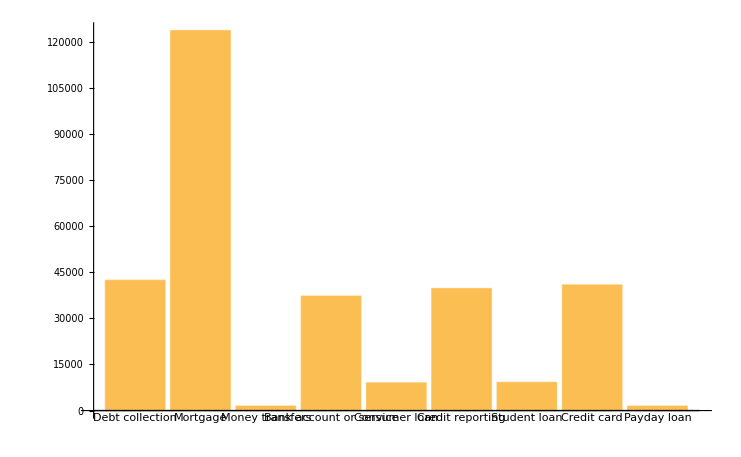

```mathematica
BarChart[Apply[Labeled,Reverse[products,2],{1}]]
```

Let’s create a neat word map. The states with higher complaints will have a larger font while the ones with less complaints will be displayed with a smaller font. First, let’s get the index of the “State” column.

```mathematica
Position[data[[1,All]],"State"]
```

{{6}}

Now we’ll Tally the states

```mathematica
states=Tally[data[[2;;,6]]];
```

Next, generate images using the Rasterize function and assign words RGB colors randomly

```mathematica
images=#2->Rasterize[Style[#1,RandomColor[LCHColor[_,1,_]]],"Image",RasterSize->100]&@@@states;
```

Now display the images with the ImageCollage function

```mathematica
ImageCollage[images,"Fit",400,ImagePadding->4,Background->White]
```

-Graphics-